## Math 137 Sp 19 Mathematica Hw 1 Ernst Differential Equations and Phase Planes

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the homework turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work. 
Each group turns in one (stapled) printout at the beginning of class.

Due: Friday, Feb 8.

### Tutorial: Fish in a Lake

Scientists use the differential equation dP/dt=0.7P (1-P/9) to predict future fish populations in Lake Minnetonka, where P represents the population in thousands of fish and t is in years.
(i) Solve the differential equation
(ii) Plot a slope field of the differential equation in a window that shows the important features.
(iii) What happens if the initial fish population is twenty thousand? forty thousand, sixty thousand, eighty thousand and one hundred thousand?

```mathematica
DSolve[P'[t]==0.7P[t](1-P[t]/9),P[t],t]
```

{{P[t]→(5.06655×10^15 2.71828^(0.7 t))/(5.6295×10^14 2.71828^(0.7 t)+2.71828^(5.06655×10^15 C[1]))}}

```mathematica
?VectorPlot
```

VectorPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}] generates a vector plot of the vector field {v_x,v_y} as a function of x and y. 
VectorPlot[{{v_x,v_y},{w_x,w_y},…},{x,x_min,x_max},{y,y_min,y_max}] plots several vector fields. 
VectorPlot[…,{x,y}∈reg] takes the variables {x,y} to be in the geometric region reg.

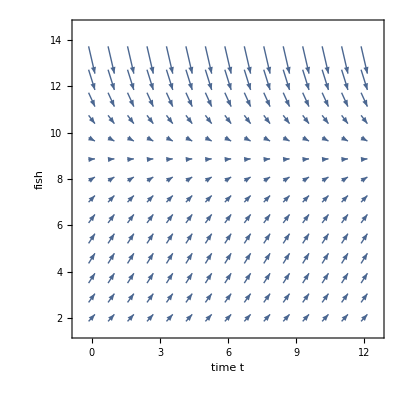

```mathematica
vectorfield=VectorPlot[{1,0.7y(1-y/9)},{t,0,12},{y,2,14},VectorStyle->Arrowheads[.03],FrameLabel->{Row[{"time t"}],Row[{"fish "}]}]
```

```mathematica
f1[t_]=P[t]/.DSolve[{P'[t]==0.7P[t](1-P[t]/9),P[0]==1},P[t],t][[1,1]]
f2[t_]=P[t]/.DSolve[{P'[t]==0.7P[t](1-P[t]/9),P[0]==4},P[t],t][[1,1]]
f3[t_]=P[t]/.DSolve[{P'[t]==0.7P[t](1-P[t]/9),P[0]==7},P[t],t][[1,1]]
f4[t_]=P[t]/.DSolve[{P'[t]==0.7P[t](1-P[t]/9),P[0]==9},P[t],t][[1,1]]
f5[t_]=P[t]/.DSolve[{P'[t]==0.7P[t](1-P[t]/9),P[0]==12},P[t],t][[1,1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5.06655×10^15 2.71828^(0.7 t))/(4.5036×10^15+5.6295×10^14 2.71828^(0.7 t))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5.06655×10^15 2.71828^(0.7 t))/(7.03687×10^14+5.6295×10^14 2.71828^(0.7 t))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5.06655×10^15 2.71828^(0.7 t))/(1.60843×10^14+5.6295×10^14 2.71828^(0.7 t))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5.06655×10^15 2.71828^(0.7 t))/(0.111111+5.6295×10^14 2.71828^(0.7 t))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5.06655×10^15 2.71828^(0.7 t))/((-1.40737×10^14-0.0452646 ⅈ)+5.6295×10^14 2.71828^(0.7 t))

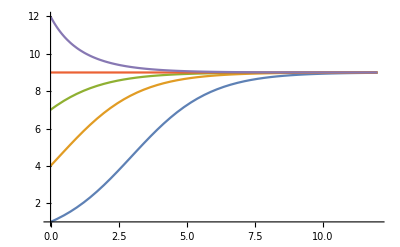

```mathematica
curveplot=Plot[{f1[t],f2[t],f3[t],f4[t],f5[t]},{t,0,12},PlotRange->All]
```

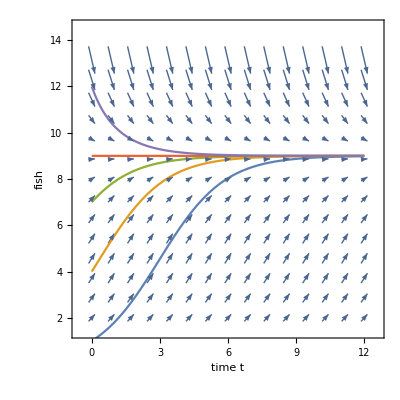

```mathematica
Show[vectorfield,curveplot]
```

### Tutorial: predator-prey model with two species, foxes and rabbits.

This Demonstration illustrates the predator-prey model with two species, foxes and rabbits. Foxes prey on rabbits that live on vegetation. 

The rabbit population is x and the fox population is y; both depend on time t.

1. In the absence of foxes, the rabbit population grows at a rate proportional to its current population; thus dx/dt=a x when y=0 with a>0.

2. In the absence of rabbits, the foxes die out; thus dy/dt=-c y when x=0 with c>0.

3. The number of encounters between the species is proportional to the product of their populations. Each encounter tends to increase y and decrease x. Thus the growth rate of x includes a term of the form -α x y and that of y includes a term of the form γ x y, where α and γ positive. The parameters a, α, c, and γ are independent of t. These assumptions lead to the equations:

dx/dt = a x-α x y=x(a-α y),

dy/dt=-c y+γ x y=y(-c+γ x).

Reference:
[1] J. R. Brannan and W. E. Boyce, Differential Equations with Boundary Value Problems: An Introduction to Modern Methods and Applications, New York: John Wiley and Sons, 2010.

Below we are solving the differential equations numerically. The starting conditions are chosen at random as {1,1}. The time interval is chosen as [start,stop] at random.

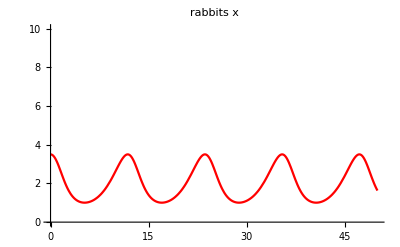

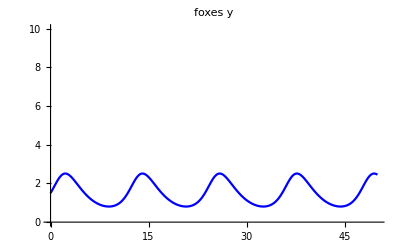

```mathematica
Clear[a,α,γ,a,b];
a=.6;
α=.4;
c=.5;
γ=.25;
start=0;
stop=50;
rabbitstart:=3.5
foxstart:=1.5
sol=NDSolve[{{x1'[t]==a*x1[t]-α*y1[t]*x1[t],y1'[t]==-c*y1[t]+γ*y1[t]*x1[t]},{x1[start]==rabbitstart,y1[start]==foxstart}},{x1[t],y1[t]},{t,start,stop}];
x2[t_]=x1[t]/.sol[[1,1]];
y2[t_]=y1[t]/.sol[[1,2]];
plotx=Plot[x2[t],{t,start,stop},PlotLabel->Row[{"rabbits ",Style["x",Italic]}],PlotStyle->Red,PlotRange->{0,10}]
ploty=Plot[y2[t],{t,start,stop},PlotLabel->Row[{"foxes ",Style["y",Italic]}],PlotStyle->Blue,PlotRange->{0,10}]
```

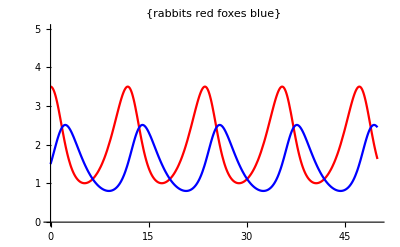

```mathematica
plotx=Plot[{x2[t],y2[t]},{t,start,stop},PlotLabel->{"rabbits red foxes blue"},PlotStyle->{Red,Blue},PlotRange->{0,5}]
```

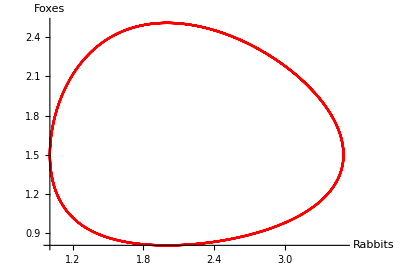

```mathematica
curveplot1=ParametricPlot[{x2[t],y2[t]},{t,0,50},PlotStyle->Red,AxesLabel->{"Rabbits","Foxes"}]
```

The command below produces the slope field of the differential equation.

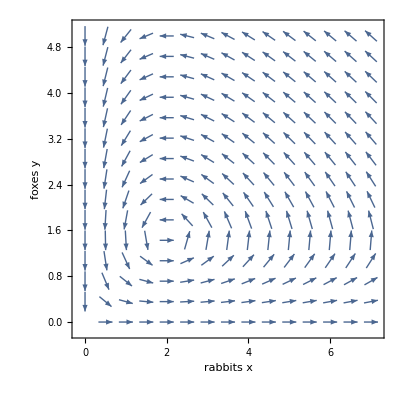

```mathematica
Clear[a,b,α,γ]
a:=.6
α:=.4
c:=.5
γ:=.25
slopefield=VectorPlot[{a*x-α*y*x,-c*y+γ*y*x},{x,0,7},{y,0,5},VectorScale->{Tiny,Automatic,None},FrameLabel->{Row[{"rabbits ",Style["x",Italic]}],Row[{"foxes ",Style["y",Italic]}]}]
```

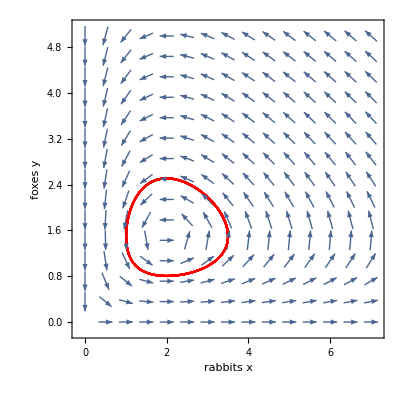

```mathematica
Show[slopefield,curveplot1]
```

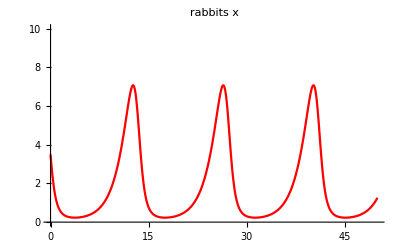

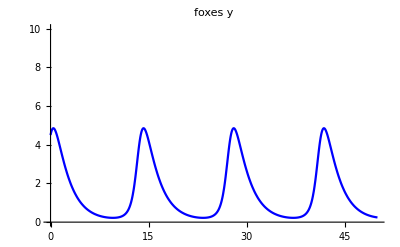

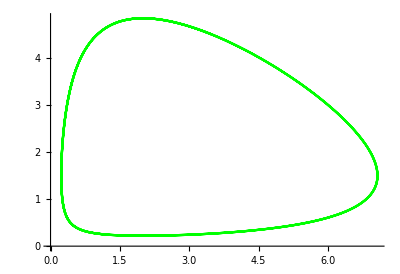

```mathematica
Clear[a,b,α,γ,a,b];
a=.6;
α=.4;
c=.5;
γ=.25;
start=0;
stop=50;
rabbitstart:=3.5
foxstart:=4.5
sol=NDSolve[{{x1'[t]==a*x1[t]-α*y1[t]*x1[t],y1'[t]==-c*y1[t]+γ*y1[t]*x1[t]},{x1[start]==rabbitstart,y1[start]==foxstart}},{x1[t],y1[t]},{t,start,stop}];
x2[t_]=x1[t]/.sol[[1,1]];
y2[t_]=y1[t]/.sol[[1,2]];
plotx=Plot[x2[t],{t,start,stop},PlotLabel->Row[{"rabbits ",Style["x",Italic]}],PlotStyle->Red,PlotRange->{0,10}]
ploty=Plot[y2[t],{t,start,stop},PlotLabel->Row[{"foxes ",Style["y",Italic]}],PlotStyle->Blue,PlotRange->{0,10}]
curveplot2=ParametricPlot[{x2[t],y2[t]},{t,0,50},PlotStyle->Green]
```

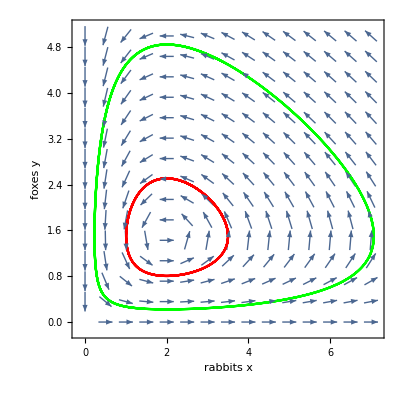

```mathematica
Show[slopefield,curveplot1,curveplot2]
```

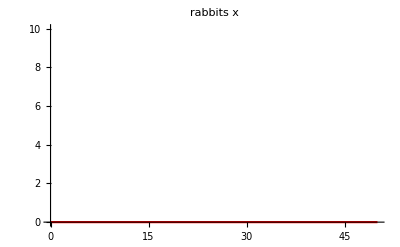

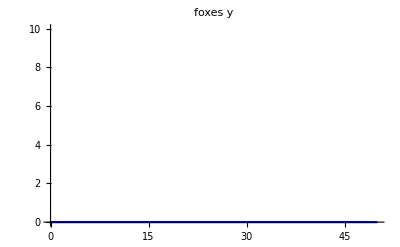

```mathematica
Clear[a,b,α,γ,a,b];
a=.6;
α=.4;
c=.5;
γ=.25;
start=0;
stop=50;
rabbitstart:=0
foxstart:=0
sol=NDSolve[{{x1'[t]==a*x1[t]-α*y1[t]*x1[t],y1'[t]==-c*y1[t]+γ*y1[t]*x1[t]},{x1[start]==rabbitstart,y1[start]==foxstart}},{x1[t],y1[t]},{t,start,stop}];
x2[t_]=x1[t]/.sol[[1,1]];
y2[t_]=y1[t]/.sol[[1,2]];
plotx=Plot[x2[t],{t,start,stop},PlotLabel->Row[{"rabbits ",Style["x",Italic]}],PlotStyle->Red,PlotRange->{0,10}]
ploty=Plot[y2[t],{t,start,stop},PlotLabel->Row[{"foxes ",Style["y",Italic]}],PlotStyle->Blue,PlotRange->{0,10}]
```

```mathematica
NSolve[{a*x-α*y*x==0,-c*y+γ*y*x==0},{x,y}]
```

{{x→2.,y→1.5},{x→0.,y→0.}}

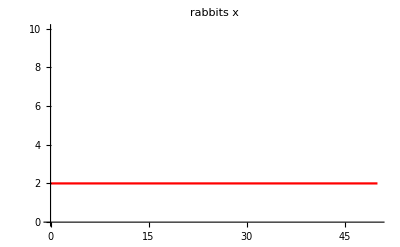

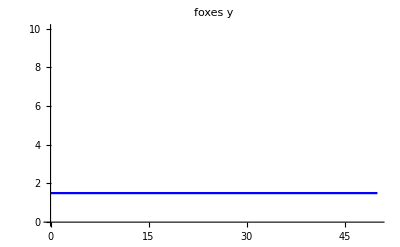

```mathematica
Clear[a,b,α,γ,a,b];
a=.6;
α=.4;
c=.5;
γ=.25;
start=0;
stop=50;
rabbitstart:=2
foxstart:=3/2
sol=NDSolve[{{x1'[t]==a*x1[t]-α*y1[t]*x1[t],y1'[t]==-c*y1[t]+γ*y1[t]*x1[t]},{x1[start]==rabbitstart,y1[start]==foxstart}},{x1[t],y1[t]},{t,start,stop}];
x2[t_]=x1[t]/.sol[[1,1]];
y2[t_]=y1[t]/.sol[[1,2]];
plotx=Plot[x2[t],{t,start,stop},PlotLabel->Row[{"rabbits ",Style["x",Italic]}],PlotStyle->Red,PlotRange->{0,10}]
ploty=Plot[y2[t],{t,start,stop},PlotLabel->Row[{"foxes ",Style["y",Italic]}],PlotStyle->Blue,PlotRange->{0,10}]
```

Note that the solutions to

```mathematica
NSolve[{a*x-α*y*x==0,-c*y+γ*y*x==0},{x,y}]
```

{{x→2.,y→1.5},{x→0.,y→0.}}

are called critical points or equilibrium points - the populations remain constant.

## Your Homework

### The drug equations

Pharmacokineticists have determined that if a given human being has a given concentration of a given drug at time t = 0, then there are always positive constants A and k such that the amount in grams y[t] of the drug in the body fluids is governed by the differential equation
        y'[t] = -(k y[t])/(A + y[t])
        with y[0] = concentration at time t = 0.

Pharmacokineticists call this model the Michaelis-Menten equation and have used it since 1913.

The original paper is Michaelis and Menten, "Die Kinetik der Invertinwirkung," Biochem Z., 49(1913), 333-369.

Before you get serious about this differential equation, there are two cases of big-time interest.

#### A Cocaine and related drugs.

(i) For drugs like cocaine, y[0] is usually very small relative to A. In fact for cocaine, if y[0] is big relative to A, then there is nothing to plot because a big y[0] is lethal.
Here is a sample with y[0] = 0.0025, A = 6, and k = 3:

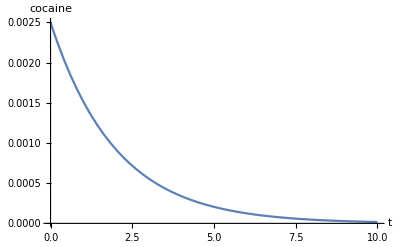

```mathematica
endtime = 10;
A = 6;
k = 3;
starter = 0.0025;
Clear[t,y,Derivative];
solution = 
 NDSolve[{y'[t] == -(k y[t])/(A+y[t]), 
            y[0] == starter},y[t],{t,0,endtime}];
coke[t_] = y[t]/.solution[[1]];

cokeplot = Plot[{coke[t]},{t,0,endtime},
       AxesLabel->{"t","cocaine"},PlotRange->All]
```

Holding the same constants, look at  the differential equation again: 
       y'[t] =-(k y[t])/(A + y[t]).
Because y[t] is very small all the time, you can expect the solution y[t] to plot out about the same as the exponential solution of
       y'[t] = -(k y[t])/(A + 0)= -k/A y[t].
Check this out.

Tip:

In case you've forgotten, the solution of  
         y'[t] = -k/A y[t] with a given y[0]
has a nice, easy formula. It is:
         y[t] = y[0] E^(-(k t)/A).
You should know this formula cold. It's a matter of basic calculus literacy.

(ii)  Do a two more samples of your own choice with y[0] small relative to A and then explain the statement: 
For studying the decay of cocaine, most pharmacokineticists are happy to replace the basic model   
            y'[t] = -(k y[t])/(A + y[t])
            with y[0] = concentration at time t = 0
by the simpler exponential model
            y'[t] =-(k y[t])/A
            with y[0] = concentration at time t = 0.

Explain why most folks say that cocaine concentration decays exponentially.

#### B Alcohol and related drugs

(i) For drugs like alcohol, y[0] is usually rather large relative to A. 
Here is a sample with y[0] = 0.025, A = 0.005, and k = 0.01:

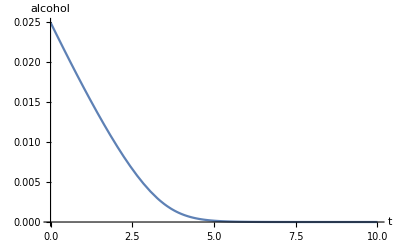

```mathematica
endtime = 10;
A = 0.005;
k = 0.01;
starter = 0.025;
solution = 
 NDSolve[{y'[t] == -(k y[t])/(A+y[t]), 
            y[0] == starter},y[t],{t,0,endtime}];
alcohol[t_] = y[t]/.solution[[1]];

sloshplot = Plot[{alcohol[t]},{t,0,endtime},
       AxesLabel->{"t","alcohol"},
       PlotRange->All]
```

Holding the same constants, look at  the differential equation  
       y'[t] = -(k y[t])/(A + y[t])
again.   Because y[t] is relatively large, you can expect  
      -(k y[t])/(A + y[t])
to be close to the global scale of  
      -(k y)/(A+y)
which is      
      -(k y)/y= -k.
As a result, you can expect the solution y[t] to plot out about the same as the line solution of
       y'[t] = -k
until y[t] has decayed to the point at which it is very small.
Check this out.

Tip:

In case you've forgotten, the solution of  
         y'[t] = -k with a given y[0]
has a nice,easy formula. It is:
         y[t] = -k t + y[0] 
You should know this formula cold. It's a matter of basic calculus literacy.

(ii) Do a two more samples of your own choice with y[0] large relative to A and then say why you think most pharmacokineticists are happy to replace the basic model   
        y'[t] =-(k y[t])/(A + y[t])
        with y[0] = concentration at time t = 0
by the simpler linear model
        y'[t] = -k
        with y[0] = concentration at time t = 0.

(iii) Explain why most folks say that alcohol concentration decays linearly until the alcohol concentration decays to the level at which no one cares.

### Epidemics

This model was developed by W, O. Kermack and A. G. McKendrick and was studied in their papers titled
"Contributions to the mathematical theory of epidemics", Proceedings of the Royal Society A, 115, 700-721 (1927); 138, 55-83 (1932); 141,94-122 (1933). It forms the base for many epidemic models used today.

The SIR model deals with disease in a closed population. This model is geared at diseases like certain strains of flu which confer immunity to those who contract the disease and recover. Put 
       Sus[t] = the number of susceptible people at time t 
												after measurements begin;
       
Inf[t] = the number of infected people at time t 
												after measurements begin;
       
Recov[t] = the number of recovered people at time t 
												after measurements begin.

The model says that there are positive constants a and b such that
       Sus'[t] = -a Sus[t] Inf[t]
       Recov'[t] = b Inf[t].
This says that the number of susceptible decreases at a rate jointly proportional to the number of susceptible and the number of infected. And this says that the recovery rate is proportional to the number of infected.

You also know that 
        Sus[t] + Inf[t] + Recov[t] =  total size of the population under study. 

For the purposes of this problem, assume that the total population stays constant.  This tells you
        Sus'[t] + Inf'[t] + Recov'[t] = 0;
so 
        Inf'[t] = -Sus'[t] - Recov'[t] 
             = a Sus[t] Inf[t] - b Inf[t].
This gives you the full SIR epidemic model:
        Sus'[t] = - a Sus[t] Inf[t],
        Inf'[t] = a Sus[t] Inf[t] - b Inf[t]
        Recov'[t] = b Inf[t].
        with Sus[0] = number of susceptibles, Inf[0] = number of infecteds,
        and Recov[0] = number of recovered at the time the measurements begin.

#### British Flu

This information was secured from the book Mathematical Biology by J. D. Murray (Springer-Verlag, 1990). For a lot more on the modeling of epidemics, see this book.

The March 4, 1978, issue of the British Medical Journal reported all the details about a flu epidemic that swept through a boarding school in early 1978. Scientists were delighted that the actual data fell in line with those predicted by the SIR model.
The model for this epidemic is:
        Sus'[t] = -a Sus[t] Inf[t],
        Inf'[t] = a Sus[t] Inf[t] - b Inf[t].
        Recov'[t] = b Inf[t] 
        with Sus[0] = 762,  Inf[0] = 1, Recov[0] = 0, 
        a = 0.00218 and b =0.44036.

One runny-nosed brat caused all the trouble.

(i) Replay this epidemic by plotting Sus[t] and Inf[t] for 0 ≤ t ≤ 14 with t measured in days.
Comment on its severity.

Tip:

Take the predator-prey code, edit it, and run it.

(ii)  Go back to the basic SIR model:
        Sus'[t] = - a Sus[t] Inf[t],
        Inf'[t] = a Sus[t] Inf[t] - b Inf[t],
        Recov'[t] = b Inf[t].
Why is it common sense that Sus'[t] < 0; so that Sus[t] goes down as time goes up?

Tip:

Once someone recovers, that person is immune.

(iii) On the basis of part (ii) above, you know that
           Sus[0] ≥ Sus[t] for t ≥ 0.
Now look at the key ingredient of the model:
 Inf'[t] = a Sus[t] Inf[t] - b Inf[t]
                = (a Sus[t] - b) Inf[t].
Explain the statements:
→ If Sus[0] < b/a, then the model predicts no epidemic because in this case Inf[t] goes down as t goes up.

→ If Sus[0] >b/a, then the model predicts that the disease will spread and the infected population will increase until S[t] gets small enough that Sus[t] <b/a. 
In other words, if Sus[0] > b/a, then an epidemic is in the cards.

(iv) Take the boarding school data and show the plots of Sus[t] and Inf[t] together with the horizontal line through {0,b/a} on the vertical axis.
Does this plot confirm the second statement in part ii)?

### Prairie Dogs and Black-Footed Ferrets.

Consider a predator-prey relation shit between Prairie Dogs (prey) and Black-Footed Ferrets (predator).
Let x(t)= Prairie Dogs at time t,
Let y(t)= Black-Footed Ferrets at time t,
where t is measured in months.
The predator-prey model is
dx/dt=0.1x-0.00009x y
dy/dt=-0.4y+0000.00004x y,
where at t=0 x=4000 and y=1000.
a. Find the critical points of the model
b. (i) Solve the system numerically for 0≤t≤240 and plot the curves for each species.
(ii) Describe the populations maximum and minium for each species.
(iii) How long does it take between two maxima for each species?
c. Plot the slope field of the equation together with your solution curve in a prey-predator plane.

### Warfare.

A scientist who tried to apply calculus to warfare in the way you will see below was F. W. Lanchester, who worked in Britain during World War I. In his honor, fancy folks call all these models by the name Lanchesterian models. The Problem below is from Calculus and Mathematica by Davis, Porta and Uhl.

1. a) The good guys and the bad guys are engaged in combat. Agree that good[t] is the number of good guys still fighting t days after combat begins, and let bad[t] be the number of bad guys still fighting t days after combat begins.
If neither side receives reinforcing troops, then why is it natural to propose a model
         good'[t] = - a bad[t]
         bad'[t] = - b good[t]
where a and b are positive numbers?

2. b.i)If the good guys bring in new troops at a rate of f[t] new troops per day and the bad guys bring in new troops at a rate of g[t] new troops per day, then why is it natural to propose a model 
         good'[t] = - a bad[t] + f[t]
         bad'[t] = - b good[t] + g[t]
where a and b are positive numbers?

b.ii)Agree that the good guys win if bad[t] becomes 0 before good[t] becomes 0 and that the bad guys win if good[t] becomes 0 before bad[t] becomes 0.
The model
         good'[t] = - 0.5 bad[t] + Sin^2[t]
         bad'[t] = - 0.5 good[t] + Cos^2[t]
with  good[0] = bad[0] = 2
suggests the situation in which the troops on both sides are equally effective and at the start (t = 0) they are of equal strength.  The main difference is that the reinforcement rates are out of phase with the bad guys holding the initial advantage because 
      Cos^2[0]= 1 > 0 = Sin^2[0].
This suggests that the good guys lose.
Check this out by plotting good[t] and bad[t] and showing both curves together in a plot.
Determine how many days pass before the good guys are gone.

b.iii) The good guys find that they lose above, so they double their reinforcements.  This gives the model:
      good'[t] = - 0.5 bad[t] + 2 Sin^2[t]
      bad'[t] = - 0.5 good[t] + Cos^2[t]
with good[0] = bad[0] = 2.
Who wins and how long does the battle last?
Check this out by plotting good[t] and bad[t] and showing both curves together in a graph.

b.iv) This time the good guys have antiquated ammunition and heavy bureaucratic problems.  As a result, their troops are only half as effective as the troops of the bad guys.  This suggests the model:
      good'[t] = -0.5 bad[t] +  2 Sin^2[t]
      bad'[t] = -0.25 good[t] + Cos^2[t]
with good[0] = bad[0] = 2.   Who wins and how long does the battle last?
Check this out by plotting good[t] and bad[t] and showing both curves together in a graph.

b.v) Again the good guys have antiquated ammunition and heavy bureaucratic problems.  As a result, their troops are only half as effective as the troops of the bad guys, so they decide to find a positive number r as small as practical such that if 
      good'[t] = - 0.5 bad[t] +  r Sin^2[t]
      bad'[t] = - 0.25 good[t] + Cos^2[t]
with good[0] = bad[0] = 2,
then the good guys do not lose during the first 15 days.    Estimate how small r can be.

Tip: Experiment with different r's.

3. c.i) Iwo Jima

This problem originates in the book  Differential Equations and Their Applications 
by Martin Braun, Springer-Verlag, 1978.    If you like this stuff, you'll want to look at this book, 
paying special attention to section 4.3.

Iwo Jima is the largest of the volcano islands in the western Pacific Ocean.  During World War II, it was a big Japanese air base. During February and March, 1945, American marines took it at great cost in a bloody assault.  If you have been to Washington, D.C., you may have seen the Iwo Jima memorial statue which depicts U.S. Marines planting the Stars and Stripes on the beach during a very bloody stage of the battle.
The Americans kept careful records during their losses, and the records confirm that the Iwo Jima battle is correctly modeled by the ideas in the Lanchesterian model above.
Here comes the nitty-gritty:
Agree that usa[t] measures the number of active American troops and japan[t] measures the number of active Japanese troops engaged in the battle t days after the battle began.
For this battle, military scientists have arrived at the model 
       usa'[t] = -0.0544 japan[t] + f[t]
       japan'[t] = -0.0106 usa[t] + g[t]
where f[t] and g[t] are the reinforcement rates.

The individual Japanese troop was 5 times more effective than the individual American troop because the 
Japanese held a defensive position.

At the beginning of the battle, 
       usa[0] = 5.4 and japan[0] = 2.15 with units measured in tens of thousands.
The reinforcement rate for Japan was  g[t] = 0. There were no Japanese reinforcements.

The Americans piled in 5.4 (tens of thousands of) troops at the beginning of the battle (t = 0), 0 extra troops during the first and second day, 0.6 troops spread out over the third day, 0 troops during the fourth and fifth days, 1.3 troops spread out over the sixth day, and no other reinforcements.

Remember that troops are measured in tens of thousands.

The Americans considered the island secure after 28 days of battle. Replay the battle of Iwo Jima by giving plots of usa[t] and japan[t] for the first 28 days.

3.c.ii) In actuality, there were 5.28 (tens of thousands) American troops in the field on day 28. Compare this with the value predicted by the model.

Tip: Don't expect the model to be totally accurate. There is always a gap between models and reality. If you got a big discrepancy, then you did something wrong.

3.c.iii) Estimate:	How many American troops were knocked out of action?
How many Japanese troops bit the dust?

3.d.i) Modifying the Battle of Iwo Jima 
Take the battle of Iwo Jima model       
        usa'[t] = -0.0544 japan[t] + f[t]
            japan'[t] = -0.0106 usa[t] + g[t]
     with  usa[0] = 5.4 and japan[0] = 2.15  where f[t] and g[t] are the reinforcement rates.
Report what might have happened if the Americans had no reinforcements. 
Would the Americans still have won in 28 days?   How long would it have taken to secure the island? 
How many American troops would have been lost?

Tip: This means f[t] = g[t] = 0 for all t's.

d.ii)  Take the battle of Iwo Jima model       
        usa'[t] = -0.0544 japan[t] + f[t]
            japan'[t] = -0.0106 usa[t] + g[t]
  with  usa[0] = 5.4 - r and japan[0] = 2.15  where f[t] and g[t] are the reinforcement rates. But go with

```mathematica
Clear[f,t]
f[t_] := 0.5 r/; t < 2;
f[t_] := 0.6/;2 <= t <= 3;
f[t_] := 0.0/;3 < t < 5;  
f[t_] := 1.3/;5 <= t <= 6;
f[t_] :=  0.0/;6 < t;
```

and:

```mathematica
Clear[g,t]
g[t_] = 0;
```

This means that you are withholding r (0 ≤ r ≤ 5.4) troops from the main assault force and are using them as reinforcements spread out over the first two days. Is there a way to set r to improve the outcome from the American point of view?

Tip: Try out a few r's and assess the results.

d.iii)  Put yourself in the role of the Japanese high command or the American high command or both and then try out possible scenarios that come to mind.